## Practice Quiz 1

### Question 1

```mathematica
a=Quantity[5.6402, "Angstroms"]
density=Quantity[2.16,"Grams"/("Centimeters")^3]
```

5.6402 Å

2.16 g/cm^3

```mathematica
mol=Quantity[57.45,"Grams"/"Moles"]/Quantity[1,"AvogadroConstant"]
```

57.45 g/(mol N_A)

```mathematica
Solve[density==N*mol/a^3,N]
```

{{N→4.06254}}

### Question 2

```mathematica
beta=81Degree
a=Quantity[4.43,"Angstroms"]
b=a
c=Quantity[6.17,"Angstroms"]
```

81 °

4.43 Å

4.43 Å

6.17 Å

```mathematica
a*b*c*Sin[beta]
```

119.595 Å^3

### Question 4

```mathematica
a=Quantity[5.431,"Angstroms"]
```

5.431 Å

```mathematica
d=a/(√(3^2+1^2+1^2))
```

1.63751 Å

```mathematica
2Pi/d
```

3.83704 /Å

## Control Quiz

### Question 1

```mathematica
a=Quantity[3.7,"Angstroms"]
b=Quantity[4.4,"Angstroms"]
c=Quantity[5.3,"Angstroms"]
```

3.7 Å

4.4 Å

5.3 Å

```mathematica
Solve[1/d^2==1/a^2+1/b^2+1/c^2,d]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{d→-2.49767×10^-10 m},{d→2.49767×10^-10 m}}

```mathematica
separation=Quantity[1.1,"Millimeters"]
detectordistance=Quantity[90,"Millimeters"]
radiation=Quantity[12.66, "Kiloelectronvolts"]
```

1.1 mm

90 mm

12.66 keV

```mathematica
thetamax=ArcTan[separation/detectordistance]/2
```

0.00611081

```mathematica
amin=(Quantity[1,"PlanckConstant""SpeedOfLight"]/radiation)/(2Sin[thetamax])
```

6.46309 h c/keV

```mathematica
UnitConvert[amin,"Angstroms"]
```

### Question 4

```mathematica
lowere=Quantity[7.5,"Kiloelectronvolts"]
uppere=Quantity[11,"Kiloelectronvolts"]
```

7.5 keV

11 keV

```mathematica
lattice=Quantity[8.5, "Angstroms"]
```

8.5 Å

```mathematica
lowerradius=UnitConvert[2Pi/(Quantity[1,"PlanckConstant""SpeedOfLight"]/lowere),1/"Angstroms"]
upperradius=UnitConvert[2Pi/(Quantity[1,"PlanckConstant""SpeedOfLight"]/uppere),1/"Angstroms"]
```

3.8008 /Å

5.574504 /Å

```mathematica
(4/3 Pi upperradius^3-4/3 Pi lowerradius^3)
```

495.625 /Å^3

```mathematica
2Pi/lattice
```

0.739198 /Å

```mathematica
(4/3 Pi upperradius^3-4/3 Pi lowerradius^3)/(8 Pi^3/lattice^3)
```

1227.07

### Question 5

```mathematica
I=0.5
Q=0.014
```

Set::wrsym: Symbol ⅈ is Protected.

0.5

0.014

```mathematica
Solve[I==Exp[-Q^2 R^2/3],R]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→-109.642+109.642 ⅈ},{R→109.642-109.642 ⅈ}}

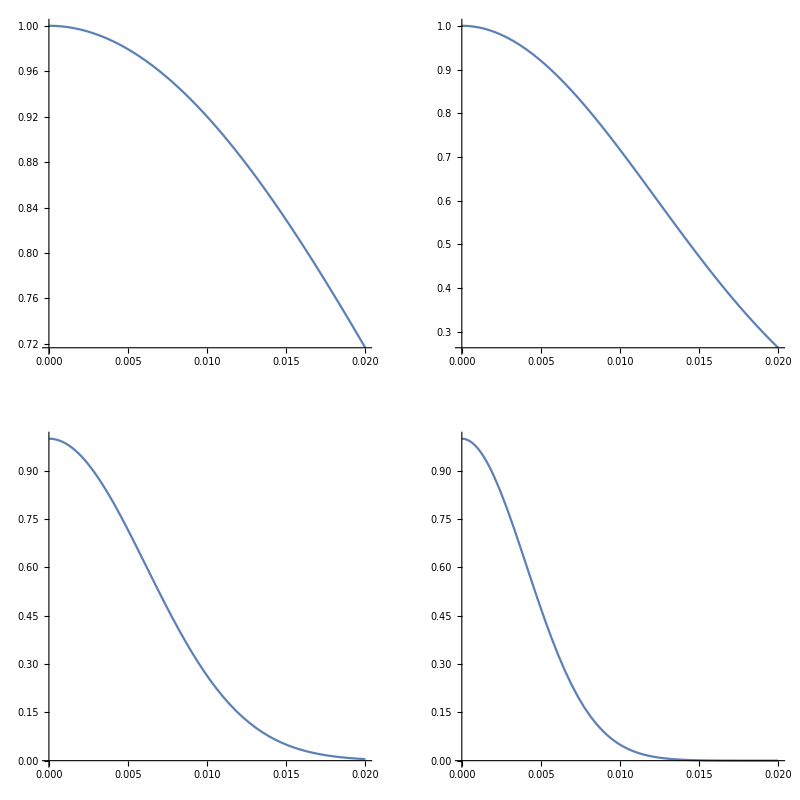

```mathematica
GraphicsGrid[{{Plot[Exp[-Q^2 50^2/3],{Q,0,0.02},AspectRatio->1],
Plot[Exp[-Q^2 100^2/3],{Q,0,0.02},AspectRatio->1]},
{Plot[Exp[-Q^2 200^2/3],{Q,0,0.02},AspectRatio->1],
Plot[Exp[-Q^2 300^2/3],{Q,0,0.02},AspectRatio->1]}}]
```